```mathematica
Mac
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
species = Import["/Users/newlocaluser/Documents/MP2/Code/species.csv"];
```

Mac

{{Acacia melanoceras,48,17,31,N/A,40},{Acalypha diversifolia,1023,582,441,N/A,20},{Adelia triloba,143,65,78,-0.67,100},{Aegiphila panamensis,40,29,11,-0.47,40},{Alchornea costaricensis,316,102,214,-2.58,200},{Alibertia edulis,417,68,349,0.62,40},{Allophylus psilospermus,111,62,49,-0.52,40},{Alseis blackiana,7928,577,7351,1.11,200},{Annona spraguei,149,14,135,-3.4,80},{Apeiba membranacea,308,97,211,-1,300},{Apeiba tibourbou,50,24,26,-2.34,80},{Aspidosperma spruceanum,473,31,442,1.28,300},{Astronium graveolens,117,21,96,0.53,300},{Beilschmiedia pendula,1996,114,1882,0.63,300},{Brosimum alicastrum,872,49,823,1.15,300},{Calophyllum longifolium,1823,13,1810,-0.03,300},{Casearia aculeata,452,78,374,1.12,50},{Casearia arborea,131,41,90,-0.32,200},{Casearia sylvestris,128,38,90,-0.07,100},{Cassipourea elliptica,1108,154,954,1.09,80},{Cavanillesia platanifolia,36,16,20,-0.24,500},{Cecropia insignis,891,82,809,-4.77,300},{Cecropia obtusifolia,264,150,114,-4.27,80},{Ceiba pentandra,62,28,34,-1.67,600},{Celtis schippii,108,20,88,0.81,160},{Chamguava schippii,541,92,449,0.61,40},{Chrysochlamys eclipes,406,282,124,N/A,20},{Chrysophyllum argenteum,711,15,696,1.05,300},{Chrysophyllum cainito,171,15,156,0.36,300},{Coccoloba coronata,138,23,115,1.42,80},{Coccoloba manzinellensis,351,11,340,2.07,100},{Cordia alliodora,189,38,151,-2.14,200},{Cordia bicolor,681,268,413,-0.79,160},{Cordia lasiocalyx,1143,214,929,-0.26,100},{Coussarea curvigemmia,2010,892,1118,0.69,30},{Croton billbergianus,631,158,473,-3.79,50},{Cupania seemannii,1271,209,1062,1.69,50},{Dendropanax arboreus,79,19,60,0,300,},{Desmopsis panamensis,11040,3383,7657,0.65,30},{Dipteryx oleifera,52,30,22,0.73,300},{Drypetes standleyi,2110,107,2003,1.17,200},{Erythrina costaricensis,68,43,25,N/A,50},{Erythroxylum macrophyllum,284,39,245,0.06,40},{Eugenia galalonensis,1975,139,1836,1.16,40},{Eugenia nesiotica,502,48,454,1.52,100},{Eugenia oerstediana,1838,38,1800,0.15,200},{Faramea occidentalis,24989,9459,15530,0.66,50},{Garcinia intermedia,4817,143,4674,1.13,100},{Guapira standleyana,155,50,105,0.82,300},{Guarea bullata,725,70,655,0.21,80},{Guarea guidonia,1889,734,1155,0.56,40},{Guatteria dumetorum,876,53,823,-0.13,300},{Guazuma ulmifolia,74,28,46,N/A,300},{Guettarda foliacea,252,59,193,0.65,100},{Gustavia superba,692,607,85,0.99,100},{Hampea appendiculata,191,36,155,-2.72,80},{Hasseltia floribunda,418,201,217,0,80},{Heisteria acuminata,94,46,48,0.73,50},{Heisteria concinna,895,196,699,0.7,150},{Hieronyma alchorneoides,118,26,92,-0.4,300},{Hirtella triandra,4407,1026,3381,0.82,80},{Hura crepitans,95,72,23,0.72,300},{Inga acuminata,606,88,518,-0.23,80},{Inga marginata,767,43,724,-1.7,300},{Inga nobilis,557,144,413,0.83,80},{Inga sapindoides,197,30,167,0.2,160},{Inga umbellifera,765,50,715,0.69,80},{Jacaranda copaia,327,167,160,-1.94,300},{Lacistema aggregatum,1264,135,1129,0.45,50},{Lacmellea panamensis,102,39,63,0.59,160},{Laetia thamnia,409,51,358,0.04,80},{Licania hypoleuca,141,15,126,1.08,80},{Lindackeria laurina,53,41,12,-0.34,100},{Lonchocarpus heptaphyllus,665,19,646,0.58,300},{Luehea seemannii,215,44,171,-1.14,300},{Macrocnemum roseum,87,29,58,1.35,80},{Maquira guianensis,1315,164,1151,0.88,100},{Maytenus schippii,76,31,45,1.13,80},{Miconia affinis,437,140,297,-1.29,40},{Miconia argentea,675,58,617,-3.3,100},{Mosannona garwoodii,502,146,356,1.5,40},{Mouriri myrtilloides,6804,2789,4015,N/A,20},{Ocotea cernua,288,87,201,0.57,40},{Ocotea oblonga,240,21,219,-1.61,300},{Ocotea whitei,390,70,320,-0.78,300},{Oenocarpus mapora,1802,1418,384,N/A,80},{Ouratea lucens,1206,198,1008,N/A,30},{Pentagonia macrophylla,306,208,98,0.87,20},{Perebea xanthochyma,226,50,176,0.72,80},{Picramnia latifolia,1080,222,858,0.42,40},{Piper arboreum,24,12,12,0.05,30},{Piper reticulatum,136,74,62,0.23,40},{Platymiscium pinnatum,164,26,138,-0.6,300},{Platypodium elegans,109,17,92,-0.36,300},{Posoqueria latifolia,73,20,53,1.4,80},{Poulsenia armata,993,61,932,-0.66,300},{Pourouma bicolor,130,10,120,-1.58,200},{Pouteria reticulata,1084,88,996,0.56,300},{Pouteria stipitata,60,23,37,0.66,160},{Prioria copaifera,1327,90,1237,1.33,600},{Protium costaricense,697,27,670,0.13,160},{Protium panamense,3020,126,2894,0.95,80},{Protium tenuifolium,2900,191,2709,0.63,200},{Psychotria grandis,57,16,41,-0.95,30},{Quararibea asterolepis,2170,338,1832,1.05,300},{Quassia amara,115,71,44,1.12,40},{Randia armata,937,472,465,0.84,50},{Rinorea sylvatica,2264,1157,1107,N/A,20},{Simarouba amara,1577,63,1514,-1.25,300},{Siparuna pauciflora,359,83,276,0.29,40},{Socratea exorrhiza,500,348,152,N/A,80},{Solanum hayesii,68,30,38,-3.18,40},{Sorocea affinis,2295,1330,965,N/A,30},{Spondias mombin,120,19,101,-1.73,300},{Spondias radlkoferi,271,25,246,-1.13,300},{Sterculia apetala,53,13,40,0.05,400},{Stylogyne turbacensis,706,110,596,N/A,30},{Tabebuia guayacan,63,16,47,1.04,300},{Tabebuia rosea,234,21,213,-0.19,300},{Tabernaemontana arborea,1732,152,1580,0.8,300},{Talisia nervosa,703,419,284,2.01,30},{Terminalia amazonia,47,16,31,0.58,300},{Terminalia oblonga,90,29,61,N/A,300},{Tetragastris panamensis,4622,125,4497,0.79,300},{Thevetia ahouai,84,64,20,N/A,20},{Trattinnickia aspera,79,15,64,N/A,300},{Trichilia pallida,472,132,340,0.07,80},{Trichilia tuberculata,10841,330,10511,0.61,300},{Triplaris cumingiana,230,48,182,-0.65,200},{Trophis caucana,136,105,31,N/A,40},{Trophis racemosa,228,28,200,0.77,80},{Unonopsis pittieri,643,217,426,0.13,80},{Virola multiflora,41,10,31,0.01,300},{Virola sebifera,1274,234,1040,0.47,200},{Virola surinamensis,178,87,91,0.04,300},{Vismia baccifera,56,39,17,-1.65,20},{Xylopia macrantha,1658,221,1437,0.69,100},{Xylosma oligandra,53,42,11,N/A,30},{Zanthoxylum acuminatum,89,13,76,-0.62,200},{Zanthoxylum ekmanii,257,92,165,-3.52,300},{Zanthoxylum panamense,241,23,218,-0.58,300}}

```mathematica
Windows

f=Import["C:/Users/Joel/Documents/CoMPLEX/MP2/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["C:/Users/Joel/Documents/CoMPLEX/MP2/bci.traits.csv"];
```

Windows

```mathematica
Data Purification
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
clusterIndices = Map[IntegerPart[#]&,Flatten[Values[Select[f,Keys[#]=="bciAdultClusterIndices10_5_141"&]]]];
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
clusterSpecies = DeleteCases[Flatten[MapIndexed[If[Length[DeleteCases[#,0]]>0,#2,0]&,B]],0];
clusters = Map[Keys[#]&,GatherBy[MapThread[#1->#2&,{clusterSpecies,clusterIndices}],Values[#]&]];
speciesMap = MapThread[#1->First[#2]&,{clusterSpecies,species}]
```

Data Purification

{2→Acacia melanoceras,3→Acalypha diversifolia,5→Adelia triloba,6→Aegiphila panamensis,7→Alchornea costaricensis,9→Alibertia edulis,10→Allophylus psilospermus,11→Alseis blackiana,17→Annona spraguei,18→Apeiba membranacea,19→Apeiba tibourbou,25→Aspidosperma spruceanum,27→Astronium graveolens,32→Beilschmiedia pendula,34→Brosimum alicastrum,36→Calophyllum longifolium,39→Casearia aculeata,40→Casearia arborea,43→Casearia sylvestris,44→Cassipourea elliptica,45→Cavanillesia platanifolia,46→Cecropia insignis,48→Cecropia obtusifolia,50→Ceiba pentandra,51→Celtis schippii,55→Chamguava schippii,57→Chrysochlamys eclipes,58→Chrysophyllum argenteum,59→Chrysophyllum cainito,63→Coccoloba coronata,64→Coccoloba manzinellensis,69→Cordia alliodora,70→Cordia bicolor,71→Cordia lasiocalyx,72→Coussarea curvigemmia,74→Croton billbergianus,78→Cupania seemannii,79→Dendropanax arboreus,80→Desmopsis panamensis,82→Dipteryx oleifera,83→Drypetes standleyi,86→Erythrina costaricensis,87→Erythroxylum macrophyllum,90→Eugenia galalonensis,91→Eugenia nesiotica,92→Eugenia oerstediana,93→Faramea occidentalis,104→Garcinia intermedia,107→Guapira standleyana,108→Guarea bullata,110→Guarea guidonia,111→Guatteria dumetorum,112→Guazuma ulmifolia,113→Guettarda foliacea,114→Gustavia superba,116→Hampea appendiculata,117→Hasseltia floribunda,118→Heisteria acuminata,119→Heisteria concinna,121→Hieronyma alchorneoides,124→Hirtella triandra,125→Hura crepitans,127→Inga acuminata,131→Inga marginata,132→Inga nobilis,137→Inga sapindoides,140→Inga umbellifera,141→Jacaranda copaia,142→Lacistema aggregatum,143→Lacmellea panamensis,145→Laetia thamnia,148→Licania hypoleuca,150→Lindackeria laurina,151→Lonchocarpus heptaphyllus,153→Luehea seemannii,155→Macrocnemum roseum,157→Maquira guianensis,160→Maytenus schippii,161→Miconia affinis,162→Miconia argentea,169→Mosannona garwoodii,170→Mouriri myrtilloides,179→Ocotea cernua,180→Ocotea oblonga,182→Ocotea whitei,183→Oenocarpus mapora,188→Ouratea lucens,192→Pentagonia macrophylla,193→Perebea xanthochyma,194→Picramnia latifolia,196→Piper arboreum,200→Piper reticulatum,202→Platymiscium pinnatum,203→Platypodium elegans,204→Posoqueria latifolia,205→Poulsenia armata,206→Pourouma bicolor,208→Pouteria reticulata,209→Pouteria stipitata,210→Prioria copaifera,212→Protium costaricense,213→Protium panamense,214→Protium tenuifolium,223→Psychotria grandis,231→Quararibea asterolepis,232→Quassia amara,233→Randia armata,235→Rinorea sylvatica,241→Simarouba amara,243→Siparuna pauciflora,245→Socratea exorrhiza,248→Solanum hayesii,250→Sorocea affinis,252→Spondias mombin,253→Spondias radlkoferi,254→Sterculia apetala,255→Stylogyne turbacensis,258→Tabebuia guayacan,259→Tabebuia rosea,260→Tabernaemontana arborea,263→Talisia nervosa,264→Terminalia amazonia,265→Terminalia oblonga,266→Tetragastris panamensis,269→Thevetia ahouai,271→Trattinnickia aspera,276→Trichilia pallida,277→Trichilia tuberculata,279→Triplaris cumingiana,280→Trophis caucana,281→Trophis racemosa,283→Unonopsis pittieri,288→Virola multiflora,289→Virola sebifera,290→Virola surinamensis,291→Vismia baccifera,295→Xylopia macrantha,296→Xylosma oligandra,297→Zanthoxylum acuminatum,298→Zanthoxylum ekmanii,299→Zanthoxylum panamense}

```mathematica
Graph Construction

Manipulate[
A = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
W = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];

An = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1<-adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
Wn = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1< -adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];
validSpecies = DeleteDuplicates[Map[Keys[#]&,A]];
validClusters = Map[Intersection[#,validSpecies]&,clusters];
gn = Graph[An,DirectedEdges->True,EdgeWeight->Abs[Wn]];
gp =Graph[A,DirectedEdges->True,EdgeWeight->W];
g = Graph[Join[An,A],DirectedEdges->True,EdgeWeight->Join[Wn,W]];
{gp,gn,g}

,{adjacencyThreshold,2.75},ControlType->InputField]
```

Construction Graph

Anton

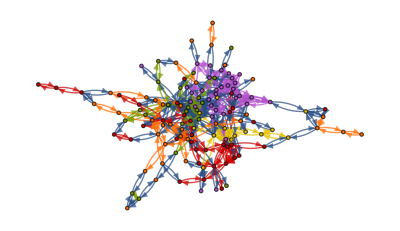

-Graphics-

```mathematica
Anton

HighlightGraph[g,Map[Subgraph[g,#]&,validClusters]]
CommunityGraphPlot[g,validClusters]
```

# Social Network Analysis

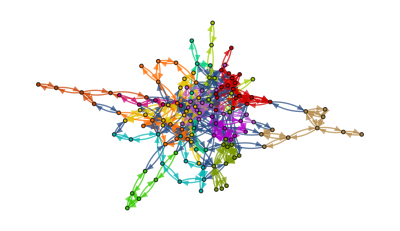

-Graphics-

```mathematica
communities = FindGraphCommunities[gp,Method->"Modularity"];
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
Trait Space
```

```mathematica
ReducedData = DimensionReduce[DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,bciTraits],Invalid],3];
```

```mathematica
Graphics3D[Map[Point[#]&,ReducedData],Axes->True]
```

-Graphics3D-